# Learning tabular data

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
?neurallogic`*
```

## Get data

```mathematica
data=ResourceData["663653b1-6151-48ad-b693-3ee813b191c6"]
```

Dataset[<>]

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

## Create feature encoders

```mathematica
Encoders[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->NetEncoder[{"Class",Last[#],"IndicatorVector"}]&/@featureValues]
]
encoders=Encoders[trainData];
inputSize=Total[First[#["Output"]]&/@Normal/@Values[Drop[encoders,-1]]];
classes=Normal[DeleteDuplicates[data[All,"Acceptability"]]];
```

```mathematica
featureLayer=NetGraph[<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[First[#]]->"Catenate"&,Drop[Normal[encoders],-1]],
"PurchasePrice"->encoders["PurchasePrice"],
"MaintenanceCost"->encoders["MaintenanceCost"],
"Doors"->encoders["Doors"],
"Passengers"->encoders["Passengers"],
"Cargo"->encoders["Cargo"],
"Safety"->encoders["Safety"]
];
```

## Create net

```mathematica
{softNet,hardNet}=Block[{numClasses=Length[classes],classificationLayerSize},
classificationLayerSize=128*numClasses;
HardNeuralChain[{
HardNeuralNAND[inputSize,classificationLayerSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
net=NetGraph[<|"FeatureLayer"->featureLayer,"SoftNet"->softNet|>,{"FeatureLayer"->"SoftNet"}];
```

```mathematica
trainableNet=NetGraph[
<|"Net"->net,"Loss"->HardClassificationLoss[]|>,
{NetPort["Acceptability"]->NetPort["Loss","Target"],"Net"->"Loss"},
"Acceptability"->encoders["Acceptability"]
];
```

## Train net

```mathematica
result=NetTrain[trainableNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
Method->{"RMSProp"},
BatchSize->Automatic,
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

## Evaluate soft net

```mathematica
trainedSoftNet=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[result["TrainedNet"]],"Loss/Error"]|>,
{},"Output"->NetDecoder[encoders["Acceptability"]]
];
```

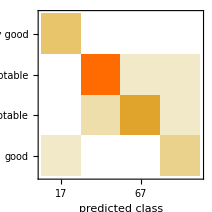
Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (98.30.7) %
Accuracy baseline | (72.52.4) %
Geometric mean of probabilities | 0.945 ± 0.012
Mean cross entropy | 0.0565 ± 0.012
Single evaluation time | 5.08 ms/example
Batch evaluation speed | 1.13 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[trainedSoftNet,testData->"Acceptability"]
```

```mathematica
trainedSoftNet2=HardNetTransformWeights[trainedSoftNet,(If[#>0.5,1,0]&)/@#&]
```

NetGraph[<>]

```mathematica
measurements=ClassifierMeasurements[trainedSoftNet2,testData->"Acceptability"]
```

Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (98.30.7) %
Accuracy baseline | (72.52.4) %
Geometric mean of probabilities | 0.945 ± 0.012
Mean cross entropy | 0.0565 ± 0.012
Single evaluation time | 5.71 ms/example
Batch evaluation speed | 1.1 examples/ms
-Graphics- |

## Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
```

```mathematica
hncwt=HardNetClassify[hnf,featureLayer,NetDecoder[encoders["Acceptability"]],testData,"Acceptability"];
```

```mathematica
hncwt2=Association[{"Prediction"->trainedSoftNet2[KeyDrop[{"Acceptability"}]@#],"Target"->#["Acceptability"]}]&/@Normal[testData];
```

```mathematica
eval=HardNetClassifyEvaluation[hncwt]
```

<|Accuracy→0.976879,Results→<|<|Prediction→unacceptable,Target→unacceptable|>→249,<|Prediction→acceptable,Target→acceptable|>→65,<|Prediction→very good,Target→very good|>→15,<|Prediction→good,Target→good|>→9,<|Prediction→unacceptable,Target→acceptable|>→2,<|Prediction→good,Target→acceptable|>→2,<|Prediction→acceptable,Target→unacceptable|>→1,<|Prediction→very good,Target→good|>→1,<|Prediction→good,Target→unacceptable|>→1,<|Prediction→good,Target→very good|>→1|>|>

```mathematica
eval2=HardNetClassifyEvaluation[hncwt2]
```

<|Accuracy→0.976879,Results→<|<|Prediction→unacceptable,Target→unacceptable|>→249,<|Prediction→acceptable,Target→acceptable|>→65,<|Prediction→very good,Target→very good|>→15,<|Prediction→good,Target→good|>→9,<|Prediction→unacceptable,Target→acceptable|>→2,<|Prediction→good,Target→acceptable|>→2,<|Prediction→acceptable,Target→unacceptable|>→1,<|Prediction→very good,Target→good|>→1,<|Prediction→good,Target→unacceptable|>→1,<|Prediction→good,Target→very good|>→1|>|>

```mathematica
Quantity[Length[Flatten[ExtractWeights[trainedSoftNet]]]/8/1024//N,"Kilobytes"]
```

1.50391 kB

```mathematica
HardNetBooleanExpression[hnf,inputSize];
```

## Train standard net

```mathematica
classifier=Classify[trainData->"Acceptability",Method->"NeuralNetwork",PerformanceGoal->"Memory"]
```

ClassifierFunction[…]

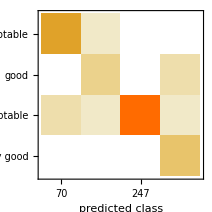
Classifier Measurements
Classifier method | NeuralNetwork
Number of test examples | 346
Accuracy | (98.00.8) %
Accuracy baseline | (72.52.4) %
Geometric mean of probabilities | 0.931 ± 0.017
Mean cross entropy | 0.0714 ± 0.018
Single evaluation time | 5.82 ms/example
Batch evaluation speed | 1.47 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[classifier,testData->"Acceptability"]
```

```mathematica
Information[classifier,"FunctionMemory"]
```

357. kB

## Notes

```mathematica
tmp1=Map[
With[{d=Drop[#,-1]},
{Flatten[Values[trainedSoftNet[d,"Probabilities"]]],Flatten[HardNetClassProbabilities[HardNetClassScores[HardNetClassBits[hnf,featureLayer,{d}]]]]}
]&,Normal[testData]];
```

```mathematica
With[{d=#},Total[d[[1]]-d[[2]]]<0.00001]&/@tmp1
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
tmp2=Map[
Block[{d=Drop[#,-1],decoder=NetDecoder[encoders["Acceptability"]]},
{decoder@Flatten[Values[trainedSoftNet[d,"Probabilities"]]],HardNetClassPrediction[HardNetClassProbabilities[HardNetClassScores[HardNetClassBits[hnf,featureLayer,{d}]]],decoder]}
]&,Normal[testData]]
```

{{acceptable,acceptable},{unacceptable,unacceptable},{very good,very good},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{acceptable,acceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{good,good},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{good,good},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{acceptable,acceptable},{acceptable,acceptable},{unacceptable,unacceptable},{good,good},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{very good,very good},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{good,good},{good,good},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{very good,very good},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{very good,very good},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{very good,very good},{unacceptable,unacceptable},{very good,very good},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{acceptable,acceptable},{very good,very good},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{good,good},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{good,good},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{very good,very good},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{good,good},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{acceptable,acceptable},{very good,very good},{unacceptable,unacceptable},{good,good},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{good,good},{unacceptable,unacceptable},{very good,very good},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{very good,very good},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{good,good},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{very good,very good},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{very good,very good},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{acceptable,acceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{very good,very good},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{acceptable,acceptable},{acceptable,acceptable},{acceptable,acceptable},{acceptable,acceptable},{very good,very good},{unacceptable,unacceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{acceptable,acceptable},{unacceptable,unacceptable},{acceptable,acceptable}}

```mathematica
With[{d=#},d[[1]]==d[[2]]]&/@tmp2
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
softWeights=Flatten[ExtractWeights[trainedSoftNet]];
```

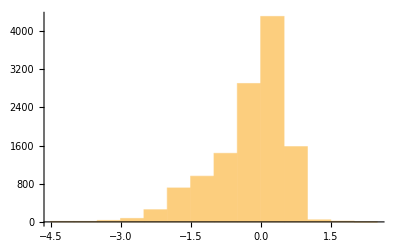

```mathematica
Histogram[softWeights,PlotRange->All]
```